```mathematica
Needs["PiCbench`"]
```

## 1- Magnitudes

```mathematica
MagnitudeList[]
```

Variable | Value | Definition
$dx | 1 | $dx=1
$nx | 1024 | $nx=1024
$qp | 0.0004 | $qp=0.0004
$mp | 0.0004 | $mp=0.0004
$np | 3000 | $np=3000
$ionMass | 1836.15 | $ionMass=1836.15
$dt | 1 | $dt=1
$a | 1 | $a=1
$b | 1 | $b=1
$c | 1 | $c=1
$charSpeed | 0.5 | $charSpeed=0.5
$charSpeedIons | 0.0116685 | $charSpeedIons:=($charSpeed)/(√($ionMass))
$lx | 1024 | $lx:=$dx $nx
$wp | 0.0342327 | $wp:=√(($np ($qp)^2 $a)/($lx $mp))
$debyeLength | 14.6059 | $debyeLength:=($charSpeed)/($wp)

```mathematica
$dx::usage
```

Length of cell size in the x dimenssion

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 14.6059 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=10;
```

```mathematica
PrintConditions[]
```

Small cell condition - ($dx<<$lx) - 1 << 1024

Small time-step condition - ($dt<<$wp^-1) - 1 << 29.2119

Big world condition - ($debyeLength<<$lx) - 292.119 << 1024

{Null,Null,Null}

```mathematica
$charSpeed=0.5;
```

## 2- Initialization

```mathematica
?UniformParticles1D
```

Generates a uniform particle distribution in [0, lx] x [-vmax,vmax].

```mathematica
UniformParticles1D[lx->$lx,vmax->$charSpeed*2,np->10]
```

{{230.188,0.0842934},{582.617,0.626044},{157.349,-0.309815},{525.253,0.320002},{954.742,-0.588959},{243.401,0.668679},{453.106,0.756058},{558.858,0.142457},{238.347,0.688969},{261.012,0.557049}}

```mathematica
electrons=UniformParticles1D[vmax->$charSpeed*2];
```

```mathematica
ions=UniformParticles1D[vmax->$charSpeedIons*2];
```

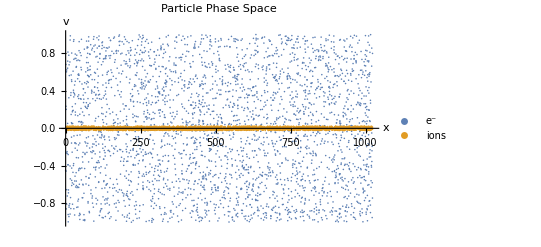

```mathematica
PhaseSpacePlot[{electrons,ions},PlotLegends->{"e^-","ions"}]
```

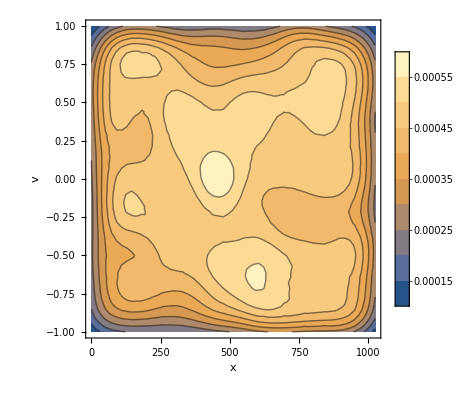

```mathematica
SmoothPhaseSpacePlot[electrons,PlotLegends->Automatic]
```